# Report Project 2

Course code: IX1501
Date: 2020-09-22

Magnus Fredriksson, magfred@kth.se
Fredrik Öberg, fobe@kth.se

Distributions

## Summary

### Task

##### Which distribution?

Together with this notebook there is a package file Project2.m with a random number generator using secret distributions. Put the package file in the same directory as this notebook and use the function randomNumber[i, n] to generate data for the distributions i=1,2,…,6. Do the following three assignments for each of the six given distributions:

Use the straight line approach to determine a distribution model.

Determine point estimates of the parameters.

Compute 95% confidence intervals for the parameters. The interval should not be longer than 10% of its mean, e.g. μ (1±0.05).

### Result

#### Part 1: Use the straight line approach to determine the given distribution models.

The following distributions where determined with the straight line approach:

	1) Exponential
	2) Geometric
	3) Gamma
	4) Normal
	5) Binomial
	6) Poisson

#### Part 2 : Determine point estimates of the parameters.

The following point estimates of the parameters where determined for the corresponding distribution:
	
	1) Lambda value of 4.47627
	2) Probability of 0.0646634
	3) Alpha value of 8.03178 and beta value of 1.6018
	4) Mean of 3.00672 and standard deviation of 5.01039
	5) n value of 11 and probability of 0.2997
	6) Mean value of 9.7949

#### Part 3 : Compute the 95 % confidence intervals for the parameters (the interval should not be longer than 10 % of its mean, e.i. μ (1 ± 0.05)).

The following lists of values represents the range of the parameters for a 95% confidence interval for the determined distributions:

       1) Lambda ϵ {4.47326, 4.49171}
	2) Probability ϵ {0.069415, 0.0697251}
	3) Alpha ϵ {7.9096, 8.04355} and beta ϵ {1.59061, 1.6153}
	4) Mean ϵ {2.99212, 3.01137}and standard deviation ϵ {4.99547, 5.00715}
	5) n ϵ {10.9502, 11.0698} and probability ϵ {0.298128, 0.301438}
	6) Mean ϵ {9.80148, 9.81295}

## Part 1: Use the straight line approach to determine the given distribution models.

#### Method

In order to determine what kind of distributions the given randomNumber function is using, we first generated 10000 samples of each of the six functions in separate lists. Those lists where sorted and plotted to get a first glance at the behaviour of the distributions. This enabled us to make educated guesses of what kind of distributions where hidden behind the data and with Mathematica’s EstimatedDistribution function we could get well estimated parameters for the distributions. Those parameters as well as the randomly generated data where then used as parameters in Mathematica’s Cumulative Distribution Function maker CDF. This function outputs a list containing the probabilities of the distribution taking the value or less of the data at the corresponding list index. If the right distribution where chosen as a parameter in EstimatedDistribution a straight line would then be able to be plotted with the values in the newly created list since they can only can be in the interval [0,1] and each value should be between the preceding as well as the subsequent value; and with this the type of distributions hidden in randomNumber could be determined.

#### Discussion

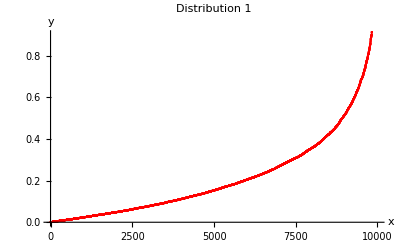
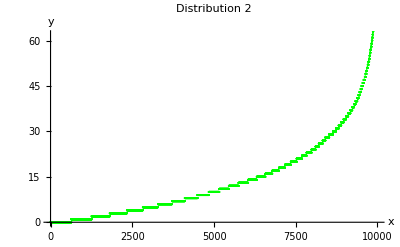
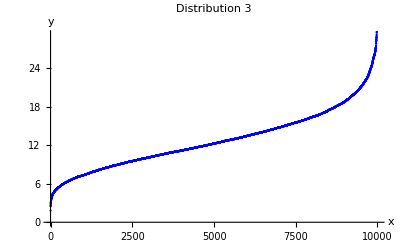
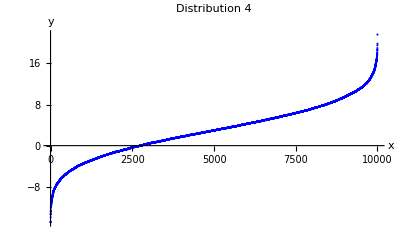
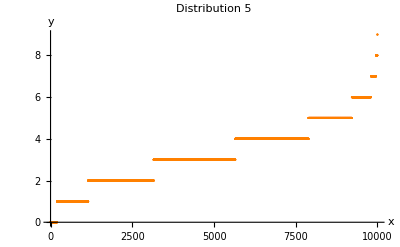
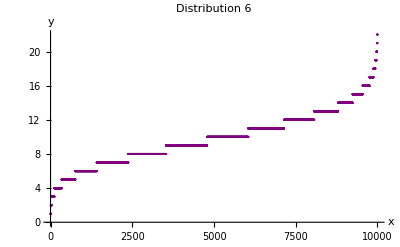
The plots of the data generated via randomNumber  came out like this:


-Graphics-

-Graphics-

-Graphics-

-Graphics-

  -Graphics-

-Graphics-

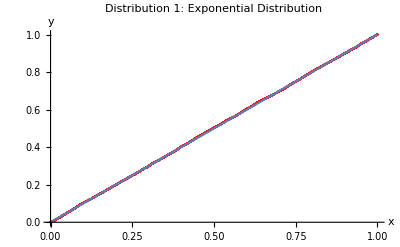
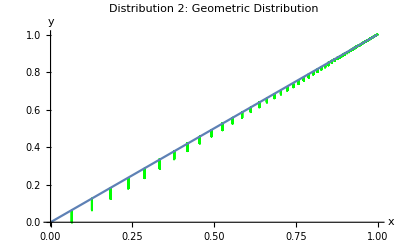
With these plots it was easy to conclude that distribution 1,3 and 4 seemed to be continuous and 2,5 and 6 discrete which limited our pool of possible distribution types. Distribution 1 and 2 is has quite the distinct look of an exponential as well as a geometric distribution so they were with no test errors concluded to be exactly those, which can be viewed in the following graphs where the data rendered via the CDF function follows a straight line almost exactly:  

-Graphics-

-Graphics-

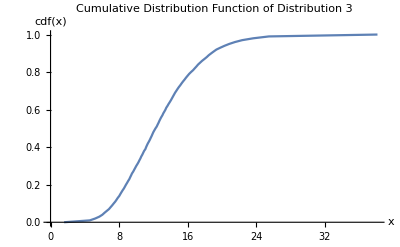
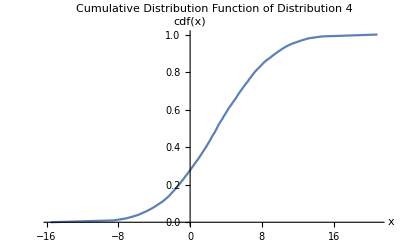
Distribution 3 and 4 seemed to be following a similar pattern as each other so a little bit of trial and error was used to be completely sure which distribution they where belonging to. First where both of their CDFs plotted:

-Graphics-

-Graphics-

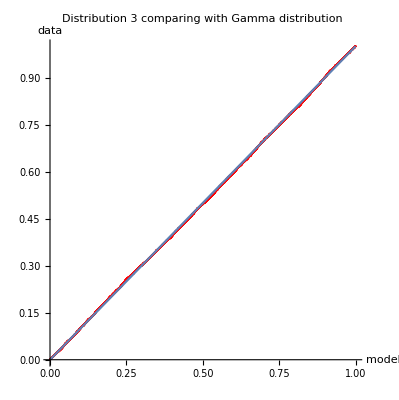
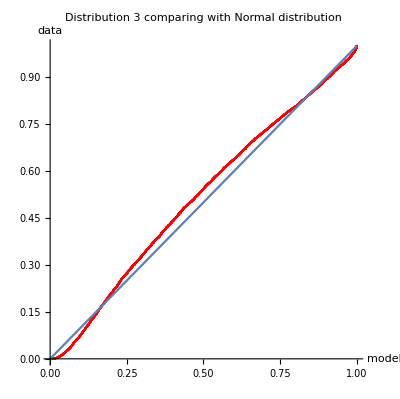
Not much more to go on there other than the negative values outputted from distribution 4, indicating it was normal distribution since gamma do not output negative values. Just to be sure were distribution 3 compared with both distribution types in the EstimatedDistribution function with the following result:

-Graphics-

-Graphics-

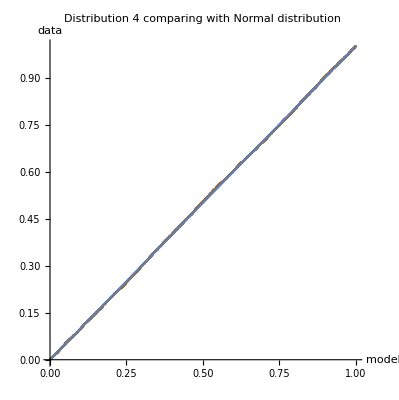
Indicating it was indeed a gamma distrubution and the following graph made us sure that distribution 4 was normal distribution since it follows the straight line almost exactly:

-Graphics-

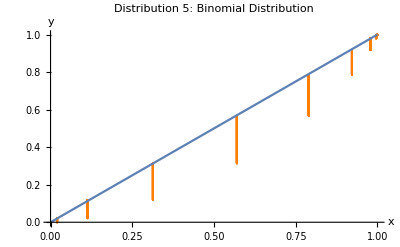
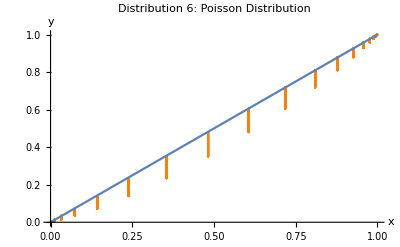
The last two graphs were assumed to be either binomial or poisson distributions since they are both discrete and follow the specific patterns of those distributions. Here we made some tests with both types of distributions and there where not huge differences between the both distributions (not suprising maybe since poisson can serve as an approximation of the binomial distribution ref: Blom page 181). But based on the following plots it was lastly concluded that distribution 5 is a binomial and distribution 6 is poisson distribution:

-Graphics-

-Graphics-

#### Conclusion

It can be concluded that the straight line approach can be used to determine a distribution model at least if the set of data is large enough. We started with a sample of 1000 but increased to 10000 to get more exact results. The user of this technique though, needs to be well versed in the world of distributions in order to be able to use it if erroneous results need to be avoided.

## Part 2: Determine point estimates of the parameters.

#### Method

When the distribution at the given index of randomNumber was established with reasonable probability it was time to estimate the parameters of those distributions, Here the Mathematica function EstimatedDistribution was used coupled with the distributions generated data and the given distribution as parameter. This functions outputs the distribution with the calculated distribution parameters which corresponds to the given data. These parameters where then extracted from the function by applying the function List on the output in order to complete the task.

#### Discussion

In order to determine that the parameters are reasonable we plot up the distributions with the calculated parameters:

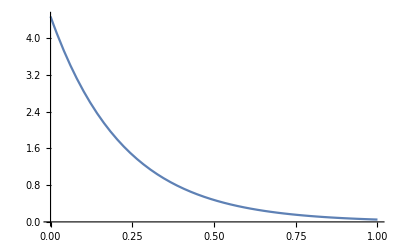

```mathematica
Plot[PDF[ExponentialDistribution[4.47627],x],{x,0,1}]
```

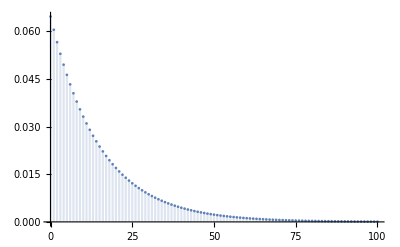

```mathematica
DiscretePlot[PDF[GeometricDistribution[0.0646634],x],{x,0,100}]
```

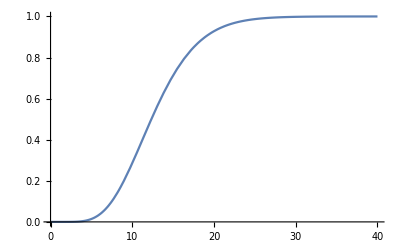

```mathematica
Plot[CDF[GammaDistribution[8.03178,1.6018],x],{x,0,40}]
```

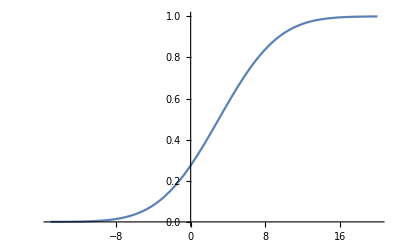

```mathematica
Plot[CDF[NormalDistribution[3.00672, 5.01039],x],{x,-15,20}]
```

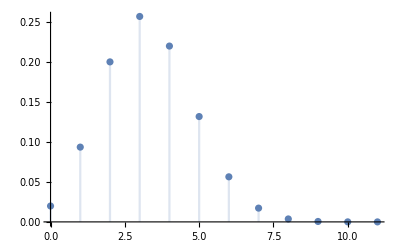

```mathematica
DiscretePlot[PDF[BinomialDistribution[11,0.2997],x],{x,0,11}]
```

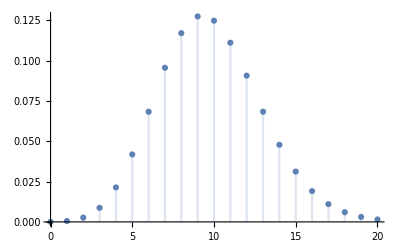

```mathematica
DiscretePlot[PDF[PoissonDistribution[9.7949],x],{x,0,20}]
```

When comparing to the result in the discussion part of Part 1 and taking to account that the exponential and geometric plots are inverted we can see that the estimated parameters seem reasonable.

#### Conclusion

Mathematica and other computational mathematical tools are great for estimating parameters to given distributions. In order to confirm that the result outputted by the programs seem to be reasonable a great deal of mathematical intuition is needed - only coming from experience in first had usage of the mathematical tools used in the background of the languages functions.

## Part 3: Compute the 95% confidence intervals for the parameters(the interval should not be longer than 10% of its mean, e.i. μ(1 ± 0.05)).

#### Method

In order to determine the 95% interval for the parameters, a number of  parameter samples were generated. The mean of those sample were calculated by using Mathematica’s MeanCI function with the generated parameter sample as well as the option ConfidenceLevel → 0.95 This function outputs two values - the top and the bottom endpoints of the confidence interval. The probability that the correct parameter value of the hidden distribution function lies within our calculated interval is 95%. In addition, we use the Assert function to ensure that the confidence interval is less than 10% of the mean, so that no such values are taken as valid.

#### Discussion

When we do an estimate we do not get the exact value we seek - that is why a confidence interval is used. This interval is based on a factor called  the “standard error”(medelfelet) and is gotten by subtracting and adding the standard error to the estimated mean creating an interval representing the range of possible values the wanted value can be from the estimation. The standard error is based on the standard deviation and the sample size and since the standard deviation in this project is unknown we therefore need an estimate for the standard deviation (D). This is calculated with the formula d = s/sqrt(n)(or in this case automatically by Mathematica’s functions). The variable s is also unknown and therefore is estimated as well.

-Graphics-

What we can conclude is that the standard error i dependent on the number n since it is divided by the square root of n. If n is large the interval becomes smaller. Since our n in this case is quite large(100) we get an confidence interval which is way below the threshold of μ(1 ± 0.05). With this we could have used a smaller sample size if this would have been a real world estimation where a larger sample size could have deemed unnecessary because of limited resources.

#### Conclusion

We have learned that the confidence interval represents the likelihood of the wanted value being inside that interval. If the interval is large the probability of the wanted value being in that interval increases and if the sample size increases the interval can be decreased since the wanted value is more likely to match the estimated value. That is a factor to keep in mind when dealing with real world problems in the future.

## Code

### Setup

```mathematica
ClearAll["`*"]
Needs["HypothesisTesting`"]
On[Assert]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Once[Get["Project2.m","IX1501"]];
```

```mathematica
n=10000;
```

```mathematica
Δ=1/n;
pdata=Δ/2+Range[0,1-Δ,Δ]//N;
```

```mathematica
lineplot=Plot[x,{x,0,1}];
```

### Distribution 1

```mathematica
d1=Sort[randomNumber[1,n]];
```

```mathematica
ListPlot[d1,AxesLabel->{HoldForm[x],HoldForm[y]},PlotStyle->Red, PlotLabel->"Distribution 1"];
```

```mathematica
estd1=EstimatedDistribution[d1,ExponentialDistribution[constant]];
(*Params for this distribution*)
paramd1 = List @@ estd1
```

{4.57759}

```mathematica
modeld1=CDF[estd1,d1];
```

```mathematica
probd1=Transpose[{modeld1,pdata}];
```

```mathematica
d1plot=ListPlot[probd1,AxesLabel->{HoldForm[x],HoldForm[y]},PlotStyle->Red, PlotLabel->"Distribution 1: Exponential Distribution"];
```

```mathematica
Show[d1plot, lineplot];
(*Generate confidence intervals*)
samples = 100;
getLambda[x_] := (List@@EstimatedDistribution[randomNumber[1,n],ExponentialDistribution[constant]])[[1]];

lambdas = {};
For[i=0,i<samples,i++,PrependTo[lambdas,getLambda[1]]]
lambdas;
ciLambda=MeanCI[lambdas, ConfidenceLevel->0.95]
```

{4.48063,4.49867}

```mathematica
Assert[Mean[lambdas]*0.1> (ciLambda[[2]]-ciLambda[[1]])];
```

### Distribution 2

```mathematica
d2=Sort[randomNumber[2,n]];
```

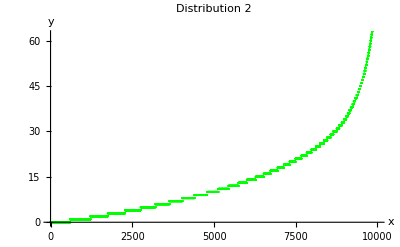

```mathematica
ListPlot[d2,AxesLabel->{HoldForm[x],HoldForm[y]},PlotStyle->Green, PlotLabel->"Distribution 2"]
```

```mathematica
estd2=EstimatedDistribution[d2,GeometricDistribution[prob]];
(*params for this distribution*)
paramd2 = estd2;
```

```mathematica
modeld2=CDF[estd2,d2];
```

```mathematica
probd2=Transpose[{modeld2,pdata}];
```

```mathematica
d2plot=ListPlot[probd2,AxesLabel->{HoldForm[x],HoldForm[y]},PlotStyle-> Green, PlotLabel->"Distribution 2: Geometric Distribution"];
```

```mathematica
(*Generate confidence intervals*)
samples = 100;
getLambda[x_] := (List@@EstimatedDistribution[randomNumber[2,n],GeometricDistribution[prob]])[[1]];

lambdas = {};
For[i=0,i<samples,i++,PrependTo[lambdas,getLambda[1]]]
lambdas;
ciLambda=MeanCI[lambdas, ConfidenceLevel->0.95]
Assert[Mean[lambdas]*0.1> (ciLambda[[2]]-ciLambda[[1]])];
Show[d2plot, lineplot];
```

{0.0648726,0.0651156}

### Distribution 3

```mathematica
d3=Sort[randomNumber[3,n]];
```

```mathematica
p=d3;
ListPlot[p,AxesLabel->{HoldForm[x],HoldForm[y]},PlotStyle->Blue,PlotLabel->"Distribution 3"];
pcdf=Table[{Quantile[p,q],q},{q,0,1,0.01}];
ListLinePlot[pcdf,AxesLabel->{HoldForm[x],HoldForm[cdf[x]]},PlotLabel->"Cumulative Distribution Function of Distribution 3"];
Δ=1/n;
𝕡data=Δ/2+Range[0,1-Δ,Δ]//N;
𝒢=EstimatedDistribution[p,GammaDistribution[α,β]];
normal =EstimatedDistribution[p,NormalDistribution[m,nd]];
(*Parameters for this distribution*)
paramd3 =List @@𝒢;
modelnd = CDF[normal,p];
modelp=CDF[𝒢,p];
comparedata=Transpose[{modelp,𝕡data}];
comparedata2 = Transpose[{modelnd, 𝕡data}];
dataplot=ListPlot[comparedata,PlotStyle->Red,AxesLabel->{"model","data"},PlotLabel->"Distribution 3 comparing with Gamma distribution",AspectRatio->Automatic];
dataplot2=ListPlot[comparedata2,PlotStyle->Red,AxesLabel->{"model","data"},PlotLabel->"Distribution 3 comparing with Normal distribution",AspectRatio->Automatic];
lineplot=Plot[x,{x,0,1}];
(*Generate confidence intervals*)
samples = 10;
getAlphaBeta[x_] := (List@@EstimatedDistribution[randomNumber[3,n],GammaDistribution[alpha, beta]]);

AlphaBetas= {};
For[i=0,i<samples,i++,PrependTo[AlphaBetas,getAlphaBeta[1]]]
AlphaBetas = Transpose[AlphaBetas];
ciAlpha=MeanCI[AlphaBetas[[1]], ConfidenceLevel->0.95]
ciBeta=MeanCI[AlphaBetas[[2]], ConfidenceLevel->0.95]
Show[dataplot,lineplot];
Show[dataplot2, lineplot];

Assert[Mean[AlphaBetas[[1]]]*0.1> (ciAlpha[[2]]-ciAlpha[[1]])];
Assert[Mean[AlphaBetas[[2]]]*0.1> (ciBeta[[2]]-ciBeta[[1]])];
```

{7.88698,8.03121}

{1.59271,1.62479}

### Distribution 4

```mathematica
d4=Sort[randomNumber[4,n]];
```

```mathematica
p=d4;
ListPlot[p,AxesLabel->{HoldForm[x],HoldForm[y]},PlotStyle->Blue,PlotLabel->"Distribution 4"];
pcdf=Table[{Quantile[p,q],q},{q,0,1,0.01}];
ListLinePlot[pcdf,AxesLabel->{HoldForm[x],HoldForm[cdf[x]]},PlotLabel->"Cumulative Distribution Function of Distribution 4"];
x=Mean[p];
s=StandardDeviation[p];
𝒩=NormalDistribution[x,s];
(*Parameters for this distribution*)
paramd4 = List @@𝒩;
modelp=CDF[𝒩,p];
Δ=1/n;
𝕡data=Δ/2+Range[0,1-Δ,Δ]//N;
comparedata=Transpose[{modelp,𝕡data}];
dataplot=ListPlot[comparedata,PlotStyle->Brown,AxesLabel->{"model","data"},PlotLabel->"Distribution 4 comparing with Normal distribution",AspectRatio->Automatic];
lineplot=Plot[x,{x,0,1}];

(*Generate confidence intervals*)
samples = 100;
getED[x_] := (List@@EstimatedDistribution[randomNumber[4,n],NormalDistribution[Expected, Deviation]]);

EDs= {};

For[i=0,i<samples,i++,PrependTo[EDs,getED[1]]]
EDs = Transpose[EDs];
ciE=MeanCI[EDs[[1]], ConfidenceLevel->0.95]
ciD=MeanCI[EDs[[2]], ConfidenceLevel->0.95]
Show[dataplot,lineplot];
Assert[Mean[EDs[[1]]]*0.1> (ciE[[2]]-ciE[[1]])];
Assert[Mean[EDs[[2]]]*0.1> (ciD[[2]]-ciD[[1]])];
```

{2.98998,3.01042}

{4.99387,5.00688}

### Distribution 5

```mathematica
d5=Sort[randomNumber[5,n]];
```

```mathematica
ListPlot[d5,AxesLabel->{HoldForm[x],HoldForm[y]},PlotStyle->Orange, PlotLabel->"Distribution 5"];
```

```mathematica
estd5=EstimatedDistribution[d5,BinomialDistribution[num,prob]];
(* Parameters for this distribution*)
paramd5 = List @@ estd5;
```

```mathematica
modeld5=CDF[estd5,d5];
```

```mathematica
probd5=Transpose[{modeld5,pdata}];
```

```mathematica
d5plot=ListPlot[probd5,AxesLabel->{HoldForm[x],HoldForm[y]},PlotStyle->Orange, PlotLabel->"Distribution 5: Binomial Distribution "];

(*Generate confidence intervals*)
samples = 100;
getNumProb[x_] := (List@@EstimatedDistribution[randomNumber[5,n],BinomialDistribution[num, prob]]);

NumProbs= {};

For[i=0,i<samples,i++,PrependTo[NumProbs,getNumProb[1]]]
NumProbs = Transpose[NumProbs];
ciNum=MeanCI[NumProbs[[1]], ConfidenceLevel->0.95]
ciProb=MeanCI[NumProbs[[2]], ConfidenceLevel->0.95]
Assert[Mean[NumProbs[[1]]]*0.1> (ciNum[[2]]-ciNum[[1]])];
Assert[Mean[NumProbs[[2]]]*0.1> (ciProb[[2]]-ciProb[[1]])];
```

{10.9637,11.0763}

{0.298035,0.301002}

```mathematica
Show[d5plot, lineplot];
```

```mathematica
paramd5
```

{11,0.301545}

### Distribution 6

```mathematica
d6=Sort[randomNumber[6,n]];
```

```mathematica
ListPlot[d6, AxesLabel->{HoldForm[x],HoldForm[y]},PlotStyle->Purple, PlotLabel->"Distribution 6"];
```

```mathematica
estd6=EstimatedDistribution[d6,PoissonDistribution[μ]];
(* Parameters for this distribution*)
paramd6 = List @@ estd6;
```

```mathematica
modeld6=CDF[estd6,d6];
```

```mathematica
probd6=Transpose[{modeld6,pdata}];
```

```mathematica
d6plot=ListPlot[probd6,AxesLabel->{HoldForm[x],HoldForm[y]},PlotStyle->Orange, PlotLabel->"Distribution 6: Poisson Distribution"];

(*Generate confidence intervals*)
samples = 100;
getMean[x_] := (List@@EstimatedDistribution[randomNumber[6,n],PoissonDistribution[μ]]);
Means= {};
For[i=0,i<samples,i++,PrependTo[Means,getMean[1]]];
ciNum=MeanCI[Means, ConfidenceLevel->0.95];
Assert[Mean[Means[[1]]]*0.1>(ciNum[[2]][[1]]-ciNum[[1]][[1]])]
```

```mathematica
Show[d6plot,lineplot];
```